# Feynman checkers: auxiliary computations M.Skopenkov, A.Ustinov

Here we check auxiliary computations in the proofs and provide a source code for the plots illustrating the main results.

```mathematica
0.Definitions
```

```mathematica
(* Evaluate this cell first *)
m=.;e=.;

theta[x,t,m,e]:=t/e ArcSin[(m e t)/(√((1+m^2 e^2)(t^2-x^2)))]-x/e ArcSin[(m e x)/(√(t^2-x^2))]+π/4;
SubPlus[f][p_]:=
1/(2Pi)(-p x+t/e ArcCos[Cos[p e]/Sqrt[1+m^2e^2]]);
SubMinus[f][p_]:=
1/(2Pi)(-p x-t/e ArcCos[Cos[p e]/Sqrt[1+m^2e^2]]);
g[p_]:=m e^2/(2Pi I Sqrt[m^2e^2+Sin[p e]^2]);
SubPlus[g][p_]:=e/(2Pi )(1+Sin[p e]/Sqrt[m^2e^2+Sin[p e]^2]);
SubMinus[g][p_]:=e/(2Pi )(1-Sin[p e]/Sqrt[m^2e^2+Sin[p e]^2]);
SubPlus[γ]=ArcSin[m e x/Sqrt[t^2-x^2]]/e;
SubMinus[γ]=-ArcSin[m e x/Sqrt[t^2-x^2]]/e;
```

```mathematica
1.Checking of Lemma Lemma 4
```

```mathematica
(* In arXiv:2007.12879v1 this was Lemma 10 *)
FullSimplify[SubPlus[f]'[p]==(-x+t Sin[p e]/ Sqrt[m^2e^2+Sin[p e]^2])/(2Pi),m>0&&e>0]
FullSimplify[SubMinus[f]'[p]==(-x-t Sin[p e]/ Sqrt[m^2e^2+Sin[p e]^2])/(2Pi),m>0&&e>0]
```

True

True

```mathematica
2.Checking of Lemma 5
```

```mathematica
(* In arXiv:2007.12879v1 this was Lemma 11 *)
mainterm=g[SubPlus[γ]]Exp[2Pi I SubPlus[f][SubPlus[γ]]+1/8]/Sqrt[SubPlus[f]''[SubPlus[γ]]]-g[SubMinus[γ]]Exp[2Pi I SubMinus[f][SubMinus[γ]]-1/8]/Sqrt[-SubMinus[f]''[SubMinus[γ]]];
gvalue=-I e Sqrt[(1-x^2/t^2)]/(2Pi);
FullSimplify[g[SubPlus[γ]]==gvalue,m>0&&e>0&&t>x>-t]      
FullSimplify[g[SubMinus[γ]]==gvalue,m>0&&e>0&&t>x>-t]   
 fvalue=t(1-x^2/t^2) Sqrt[1-(1+m^2e^2)x^2/t^2]/(2Pi m );
FullSimplify[SubPlus[f]''[SubPlus[γ]] ==fvalue,m>0&&e>0&&t>Sqrt[1+m^2e^2]x>-t&&t>x>-t]     
FullSimplify[SubMinus[f]''[SubMinus[γ]]==-fvalue,m>0&&e>0&&t>Sqrt[1+m^2e^2]x>-t&&t>x>-t]     
ratio=-I e Sqrt[m/(2Pi t )](1-(1+m^2e^2)x^2/t^2)^(-1/4);

FullSimplify[ratio==gvalue/Sqrt[fvalue],m>0&&e>0&&t>0&&1-(1+m^2e^2)x^2/t^2>0]     

thetavalue=t/e ArcCos[(√(t^2-(1+e^2 m^2 )x^2))/(√((1+m^2 e^2)(t^2-x^2)))]-x/e ArcSin[(m e x)/(√(t^2-x^2))]+π/4;
FullSimplify[Sin[(thetavalue+x/e ArcSin[(m e x)/(√(t^2-x^2))]-π/4)e/t]==Sin[(theta[x,t,m,e]+x/e ArcSin[(m e x)/(√(t^2-x^2))]-π/4)e/t],m>0&&e>0&&t>0&&t>Sqrt[1+m^2e^2]x>-t&&t>x>-t]
FullSimplify[SubPlus[f][SubPlus[γ]]==(thetavalue-π/4)/(2Pi ),m>0&&e>0&&t>Sqrt[1+m^2e^2]x>-t&&t>x>-t]
FullSimplify[SubMinus[f][SubMinus[γ]]==-(thetavalue-π/4)/(2Pi  ),m>0&&e>0&&t>Sqrt[1+m^2e^2]x>-t&&t>x>-t]
FullSimplify[Exp[2Pi I( (θ-π/4)/(2Pi )+1/8)]-Exp[2Pi I (-(θ-π/4)/(2Pi )-1/8)]==2 I Sin [θ],θ>0]
maintermvalue=ratio 2I Sin[θ];
FullSimplify[maintermvalue== e Sqrt[2m/(Pi t )](1-(1+m^2e^2)x^2/t^2)^(-1/4) Sin[θ]]
(*FullSimplify[mainterm==e Sqrt[2 m/Pi](t^2-(1+m^2e^2)x^2)^(-1/4)Sin theta[x,t,m,e],m>0&&e>0&&t>x]*)
```

True

True

True

«7 more identical outputs»

```mathematica
3.Checking of Lemma 6
```

```mathematica
(* In arXiv:2007.12879v1 this was Lemma 12 *)
g1value=-(m e^3 Sin[ p e]Cos[p e])/(2Pi I(m^2 e^2 +Sin[e p]^2)^(3/2));
FullSimplify[g'[p]==g1value,m>0&&e>0&&-Pi/2<p e<Pi/2]
g2value=-(m e^4 (m^2 e^2+Sin[ p e]^4-2(1+m^2 e^2)Sin[p e]^2))/(2Pi I(m^2 e^2 +Sin[e p]^2)^(5/2));
FullSimplify[g''[p]==g2value,m>0&&e>0&&-Pi/2<p e<Pi/2]
g3value=(m e^5 Sin[ p e]Cos[p e](4 m^4 e^4+9 m^2 e^2+Sin[ p e]^4-(6+10 m^2 e^2)Sin[p e]^2))/(2Pi I(m^2 e^2 +Sin[e p]^2)^(7/2));
FullSimplify[g'''[p]==g3value,m>0&&e>0&&-Pi/2<p e<Pi/2]
f2value=(m^2 e^3 t Cos[p e])/(2Pi (m^2 e^2 +Sin[e p]^2)^(3/2));
FullSimplify[SubPlus[f]''[p]==f2value,m>0&&e>0&&-Pi/2<p e<Pi/2]
FullSimplify[SubMinus[f]''[p]==-f2value,m>0&&e>0&&-Pi/2<p e<Pi/2]
f3value=-(m^2 e^4 t Sin[ p e](m^2 e^2+Cos[ 2p e]+2))/(2Pi(m^2 e^2 +Sin[e p]^2)^(5/2));
FullSimplify[SubPlus[f]'''[p]==f3value,m>0&&e>0&&-Pi/2<p e<Pi/2]
f4value=-(m^2 e^5 t Cos[ p e](m^4 e^4+3 m^2 e^2+4 Sin[ p e]^4-2(6+5 m^2 e^2)Sin[p e]^2))/(2Pi(m^2 e^2 +Sin[e p]^2)^(7/2));
FullSimplify[SubPlus[f]''''[p]==f4value,m>0&&e>0&&-Pi/2<p e<Pi/2]
```

True

True

True

«4 more identical outputs»

```mathematica
4.Checking of Lemma 9
```

```mathematica
(* In arXiv:2007.12879v1 this was Lemma 15 *)
FullSimplify[(μ^4u/τ^2(1+μ/n)^2(1/(γ-α)^3+1/(β-γ)^3+Sqrt[τ]/μ^3)/.{μ->m,τ->m t,n->m,α->γ-m δ/2,β->γ+m δ/2,u->ϵ})<(4 ϵ(1+16/(c^(1/2) δ^3)))/(m^(1/2) t^(3/2)),δ>0&&ϵ>0&&m>0&&t>0&& t>c/m&&√c<√(m t)&&c>0]
```

True

```mathematica
5.Checking of Lemma 11
```

```mathematica
(* In arXiv:2007.12879v1 this was Lemma 17 *)
boundaryterm=g[Pi/(2e)]Exp[2Pi I SubPlus[f][Pi/(2e)]]/(2Pi I SubPlus[f]'[Pi/(2e)])-
g[-Pi/(2e)]Exp[2Pi I SubPlus[f][-Pi/(2e)]]/(2Pi I SubPlus[f]'[-Pi/(2e)])-g[Pi/(2e)]Exp[2Pi I SubMinus[f][Pi/(2e)]]/(2Pi I SubMinus[f]'[Pi/(2e)])+
g[-Pi/(2e)]Exp[2Pi I SubMinus[f][-Pi/(2e)]]/(2Pi I SubMinus[f]'[-Pi/(2e)]);
FullSimplify[boundaryterm==0,Element[x/(2e),Integers]&&Element[(t+e)/(2e),Integers]]
FullSimplify[boundaryterm==0,Element[t/(2e),Integers]&&Element[(x+e)/(2e),Integers]]
```

True

True

```mathematica
6.Checking of Lemma 13
```

```mathematica
(* In arXiv:2007.12879v1 this was Lemma 19 *)
FullSimplify[(τ u/μ^2(1+μ/n+μ^3minf/(n^2τ ))/minf^3/.{μ->m,τ->m t,n->m,u->ϵ,minf->t δ^(5/2)/(48Pi)})<(2304 π^2 (96 π+1) ϵ)/(m t^2 δ^(15/2)),ϵ>0&&m>0&&t>0&&0<δ<1]
```

True

```mathematica
7.Checking of Lemma 15
```

```mathematica
(* In arXiv:2007.12879v1 this was Lemma 21 *)
FullSimplify[(τ u/μ^2(1+μ/n+μ^3minf/(n^2τ ))/minf^3/.{μ->m k,τ->m t/k,n->m k,u->ϵ/k,minf->t δ^(5/2)/(48Pi)})<=(2304 π^2 (96 π+δ^(5/2)) ϵ)/(k^2 m t^2 δ^(15/2)),ϵ>0&&m>0&&t>0&&k≥1&&0<δ<1]
FullSimplify[(2304 π^2 (96 π+δ^(5/2)) ϵ)/(k^2 m t^2 δ^(15/2))<(2304 π^2 (96 π+1) ϵ)/(k^2 m t^2 δ^(15/2)) ,ϵ>0&&m>0&&t>0&&k≥1&&0<δ<1]
```

True

True

```mathematica
8.Checking of Remark 8
```

```mathematica
(* In arXiv:2007.12879v1 this was Lemma 23 *)
FullSimplify[(τ u/μ^2(1+μ/n+μ^3minf/(n^2τ ))/minf^3/.{μ->m k,τ->m t/k,n->m k,u->ϵ/k,minf->t δ/(2Pi)})<=(4 π^2 (4 π+ δ) ϵ)/(k^2 m t^2 δ^3),ϵ>0&&m>0&&t>0&&k≥1&&0<δ<1]
FullSimplify[(4 π^2 (4 π+ δ) ϵ)/(k^2 m t^2 δ^3)<=(4 π^2 (4 π+ 1) ϵ)/(k^2 m t^2 δ^3),ϵ>0&&m>0&&t>0&&k≥1&&0<δ<1]
```

True

True

```mathematica
9.Checking of Lemma 18
```

```mathematica
(* In arXiv:2007.12879v1 this was Lemma 26 *)
gg[p_]:=m e^2/(Pi t)(1-4n e^2 p^2/t^2)^(-1/2);
FullSimplify[gg'[p]==4m e^4n p/(Pi t^3)(1-4n e^2 p^2/t^2)^(-3/2),1>4n e^2 p^2/t^2&&t>0&&n>1&&e>0]
FullSimplify[gg''[p]==4m e^4n (8e^2n p^2+t^2)/(Pi t^5)(1-4n e^2 p^2/t^2)^(-5/2),1>4n e^2 p^2/t^2&&t>0&&n>1&&e>0]
ff[p_]:=-t/(Pi e)ArcSin[(m e t)/(√(n(t^2-4p^2e^2)))]+(2 p/Pi )ArcSin[(2 m e^2 p)/(√(t^2-4p^2e^2))];
ff1[p_]:= (2/Pi)ArcSin[(2 e^2 m p)/(√(t^2-4 e^2 p^2))];
FullSimplify[ff'[p]== ff1[p],1>4n e^2 p^2/t^2&&1>4 e^2 p^2/t^2&&t>0&&n==1+m^2e^2&&n>0&&e>0]
FullSimplify[ff1'[p]== 4m e^2/(Pi t)(1-4e^2 p^2/t^2)^(-1)(1-4n e^2 p^2/t^2)^(-1/2),1>4n e^2 p^2/t^2&&1>4 e^2 p^2/t^2&&t>0&&n==1+m^2e^2&&e>0]

FullSimplify[ff1''[p]==16m e^4((n+2)p t^2-12n e^2p^3)/(Pi t^5)(1-4e^2 p^2/t^2)^(-2)(1-4n e^2 p^2/t^2)^(-3/2),1>4n e^2 p^2/t^2&&1>4 e^2 p^2/t^2&&t>0&&n==1+m^2e^2&&e>0]
FullSimplify[ff1'''[p]==16m e^4(768n^2 e^6p^6-48n(2n+5)e^4p^4 t^2+8(n^2-n+3)e^2p^2 t^4+(n+2)t^6)/(Pi t^9)(1-4e^2 p^2/t^2)^(-3)(1-4n e^2 p^2/t^2)^(-5/2),1>4n e^2 p^2/t^2&&1>4 e^2 p^2/t^2&&t>0&&n==1+m^2e^2&&e>0]
```

True

True

True

«3 more identical outputs»

```mathematica
10.Checking of auxiliary assertion
```

```mathematica
(* In arXiv:2007.12879v1 this was Lemma 6 *)
p=.;
c=ArcTan[Sqrt[k/(n-k)]];
z1[p_]:=p Cot[c]-p^2/2-p^3Cot[c]/6;
z2[p_]:=-p Tan[c]-p^2/2+p^3Tan[c]/6;
expansion=Expand[k(z1[p]-z1[p]^2/2+z1[p]^3/3)+(n-k)(z2[p]-z2[p]^2/2+z2[p]^3/3)];
FullSimplify[Coefficient[expansion,p,2]==-n,k>0&&n-k>0]
FullSimplify[Coefficient[expansion,p,3]==(n (n-2 k))/(3 √(k (-k+n))),k>0&&n-k>0]
FullSimplify[Coefficient[expansion,p,4]==-(11 n)/24,k>0&&n-k>0]
```

True

True

True

```mathematica
11.Checking of Proposition 10
```

```mathematica
m=.;e=.;
a1[x_,y_]:=(1/(1+m^2e^2)^((y/e-1)/2))If [Abs[x/e]≥Abs[y/e]||OddQ[x/e+y/e],0,Sum[Binomial[(x+y-2e)/(2e),r]Binomial[(y-x-2e)/(2e),r](m e)^(2r+1)(-1)^r,{r,0,y/(2e)}]];
a2[x_,y_]:=(1/(1+m^2e^2)^((y/e-1)/2)) If[x==y,1,
If [Abs[x/e]≥Abs[y/e]||OddQ[x/e+y/e],0,
Sum[Binomial[(x+y-2e)/(2e),r]Binomial[(y-x-2e)/(2e),r-1](m e)^(2r)(-1)^r,{r,1,y/(2e)}]]];
Table[FullSimplify[(x e+e)((x e-e)^2-(t e-e)^2)a1[x e-2e,t e] +(x e-e) ((x e+e)^2-(t e-e)^2)a1[x e+2e,t e]==2(x e) ((1+2 m^2 e^2)((x e)^2-e^2 )-(t e-e)^2  )a1[x e,t e],e>0],{t,1,8},{x,-8 ,8}]//MatrixForm
Table[FullSimplify[x e((x e-2e)^2-(t e)^2)a2[x e-2e,t e] +(x e-2e) ((x e)^2-(t e-2e)^2)a2[x e+2e,t e] == 2(x e-e) ((1+2 m^2 e^2)((x e)^2-2e^2 x)+2e^2 t-(t e)^2  )a2[x e,t e],e>0],{t,1,8},{x,-8 ,8}]//MatrixForm
```

(True | True | True | True | True | True | True | True | True | True | True | True | True | True | True | True | True
True | True | True | True | True | True | True | True | True | True | True | True | True | True | True | True | True
True | True | True | True | True | True | True | True | True | True | True | True | True | True | True | True | True
True | True | True | True | True | True | True | True | True | True | True | True | True | True | True | True | True
True | True | True | True | True | True | True | True | True | True | True | True | True | True | True | True | True
True | True | True | True | True | True | True | True | True | True | True | True | True | True | True | True | True
True | True | True | True | True | True | True | True | True | True | True | True | True | True | True | True | True
True | True | True | True | True | True | True | True | True | True | True | True | True | True | True | True | True)

(True | True | True | True | True | True | True | True | True | True | True | True | True | True | True | True | True
True | True | True | True | True | True | True | True | True | True | True | True | True | True | True | True | True
True | True | True | True | True | True | True | True | True | True | True | True | True | True | True | True | True
True | True | True | True | True | True | True | True | True | True | True | True | True | True | True | True | True
True | True | True | True | True | True | True | True | True | True | True | True | True | True | True | True | True
True | True | True | True | True | True | True | True | True | True | True | True | True | True | True | True | True
True | True | True | True | True | True | True | True | True | True | True | True | True | True | True | True | True
True | True | True | True | True | True | True | True | True | True | True | True | True | True | True | True | True)

```mathematica
12.Checking of Proposition 16
```

```mathematica
w=.;p=.;y=.;
a1a[x_,y_]:=Cos[alpha/2]Exp[I p x+I w y];
a2a[x_,y_]:= I Sin[alpha/2]Exp[I p x+I w y];
a1b[x_,y_]:=Sin[alpha/2]Exp[I p x-I w y];
a2b[x_,y_]:=-I Cos[alpha/2]Exp[I p x-I w y];
dirac2a=FullSimplify[(Sqrt[1+m^2 e^2]a2a[x,y+e]-a2a[x-e,y]+m e a1a[x,y])Exp[-I p x-I w y]Sin[w e]/(-I e m)/.{Sin[alpha/2]->m e/(Sqrt[1+m^2 e^2]Sin [w e]),Cos[alpha/2]->(1+Sin[p e]/(Sqrt[1+m^2 e^2]Sin [w e]))}];
FullSimplify[(dirac2a/.Cos[e w]->Cos[e p]/Sqrt[1+m^2 e^2])==0]
dirac1a=FullSimplify[(Sqrt[1+m^2 e^2] a1a[x,y+e]-a1a[x+e,y]-m e a2a[x,y])Exp[-I p x-I  w y]/.{Sin[alpha/2]->m e/(Sqrt[1+m^2 e^2]),Cos[alpha/2]->(Sin[w e]+Sin[p e]/(Sqrt[1+m^2 e^2]))}];
intermediateresult1=FullSimplify[(dirac1a/.{Cos[e w]->Cos[e p]/Sqrt[1+m^2 e^2],ⅇ^(ⅈ e w)->Cos[p e]/(Sqrt[1+m^2 e^2])+I Sin[w e]})];
FullSimplify[(intermediateresult1/.Cos[2e w]->2(Cos[e p]/Sqrt[1+m^2 e^2])^2-1)==0]
dirac2b=FullSimplify[(Sqrt[1+m^2 e^2]a2b[x,y+e]-a2b[x-e,y]+m e a1b[x,y])Exp[-I p x+I w y]Sin[w e]/(-I e m)/.{Sin[alpha/2]->m e/(Sqrt[1+m^2 e^2]Sin [w e]),Cos[alpha/2]->(1+Sin[p e]/(Sqrt[1+m^2 e^2]Sin [w e]))}];
intermediateresult2=FullSimplify[(dirac2b/.ⅇ^(-ⅈ e w)->Cos[p e]/(Sqrt[1+m^2 e^2])-I Sin[w e])];
FullSimplify[(intermediateresult2/.Cos[2e w]->2(Cos[e p]/Sqrt[1+m^2 e^2])^2-1)==0]
dirac1b=FullSimplify[(Sqrt[1+m^2 e^2] a1b[x,y+e]-a1b[x+e,y]-m e a2b[x,y])Exp[-I p x+I  w y]/.{Sin[alpha/2]->m e/(Sqrt[1+m^2 e^2]),Cos[alpha/2]->(Sin[w e]+Sin[p e]/(Sqrt[1+m^2 e^2]))}];
FullSimplify[(dirac1b/.{Cos[e w]->Cos[e p]/Sqrt[1+m^2 e^2],ⅇ^(ⅈ e w)->Cos[p e]/(Sqrt[1+m^2 e^2])+I Sin[w e]})==0]
```

True

True

True

«1 more identical outputs»

```mathematica
13.Checking an analogue of Lemma 5 for a2
```

```mathematica
(* In arXiv:2007.12879v1 this was analogue of Lemma 11 *)
mainterm=SubPlus[g][SubPlus[γ]]Exp[2Pi I SubPlus[f][SubPlus[γ]]+1/8]/Sqrt[SubPlus[f]''[SubPlus[γ]]]+SubMinus[g][SubMinus[γ]]Exp[2Pi I SubMinus[f][SubMinus[γ]]-1/8]/Sqrt[-SubMinus[f]''[SubMinus[γ]]];
gvalue=(e (t+x))/(2 π t);
FullSimplify[SubPlus[g][SubPlus[γ]]==gvalue,m>0&&e>0&&t>x>-t]      
FullSimplify[SubMinus[g][SubMinus[γ]]==gvalue,m>0&&e>0&&t>x>-t]   
 fvalue=t(1-x^2/t^2) Sqrt[1-(1+m^2e^2)x^2/t^2]/(2Pi m );
FullSimplify[SubPlus[f]''[SubPlus[γ]] ==fvalue,m>0&&e>0&&t>Sqrt[1+m^2e^2]x>-t&&t>x>-t]     
FullSimplify[SubMinus[f]''[SubMinus[γ]]==-fvalue,m>0&&e>0&&t>Sqrt[1+m^2e^2]x>-t&&t>x>-t]     
ratio= e Sqrt[m/(2Pi t )]Sqrt[(t+x)/(t-x)](1-(1+m^2e^2)x^2/t^2)^(-1/4);

FullSimplify[gvalue/Sqrt[fvalue]==ratio,m>0&&e>0&&t>0&&1-(1+m^2e^2)x^2/t^2>0]     

thetavalue=t/e ArcCos[(√(t^2-(1+e^2 m^2 )x^2))/(√((1+m^2 e^2)(t^2-x^2)))]-x/e ArcSin[(m e x)/(√(t^2-x^2))]+π/4;
FullSimplify[Sin[(thetavalue+x/e ArcSin[(m e x)/(√(t^2-x^2))]-π/4)e/t]==Sin[(theta[x,t,m,e]+x/e ArcSin[(m e x)/(√(t^2-x^2))]-π/4)e/t],m>0&&e>0&&t>0&&t>Sqrt[1+m^2e^2]x>-t&&t>x>-t]
FullSimplify[SubPlus[f][SubPlus[γ]]==(thetavalue-π/4)/(2Pi ),m>0&&e>0&&t>Sqrt[1+m^2e^2]x>-t&&t>x>-t]
FullSimplify[SubMinus[f][SubMinus[γ]]==-(thetavalue-π/4)/(2Pi  ),m>0&&e>0&&t>Sqrt[1+m^2e^2]x>-t&&t>x>-t]
FullSimplify[Exp[2Pi I( (θ-π/4)/(2Pi )+1/8)]+Exp[2Pi I (-(θ-π/4)/(2Pi )-1/8)]==2 Cos[θ],θ>0]
maintermvalue=ratio 2 Cos[θ];
FullSimplify[maintermvalue== e Sqrt[2m/(Pi t )]Sqrt[(t+x)/(t-x)](1-(1+m^2e^2)x^2/t^2)^(-1/4) Cos[θ]]
```

True

True

True

«7 more identical outputs»

```mathematica
14.Computation of Table 5
```

```mathematica
(* In arXiv:2007.12879v1 this was Table 3 *)
delta=2/10;
nmax=50; (* even number, =1/ϵ *)
m=10; (* mass *)
SubPlus[kernel][n_,k_]:=((nmax/2)/(1+m^2/nmax^2)^((n-1)/2))If[k==n,1,Sum[Binomial[(n+k)/2-1,r]Binomial[(n-k)/2-1,r-1](m/nmax)^(2r)(-1)^r,{r,1,n/2}]];
SubMinus[kernel][n_,k_]:=((nmax/2)/(1+m^2/nmax^2)^((n-1)/2))If[k==n,0,Sum[Binomial[(n+k)/2-1,r]Binomial[(n-k)/2-1,r](m/nmax)^(2r+1)(-1)^r,{r,0,n/2}]];
SubPlus[TableK]=Table[SubPlus[kernel][nmax,k],{k,2-nmax,nmax-2,2}];
SubMinus[TableK]=Table[SubMinus[kernel][nmax,k],{k,2-nmax,nmax-2,2}];
SubMinus[limitk][n_,k_]:=(m/2)BesselJ[0,m Sqrt[n^2-k^2]/nmax];
SubMinus[TableLimitK]=Table[N[SubMinus[limitk][nmax,k]],{k,2-nmax,nmax-2,2}];
SubPlus[limitk][n_,k_]:=-(m/2)((n+k)/Sqrt[n^2-k^2])BesselJ[1,m Sqrt[n^2-k^2]/nmax];

SubPlus[TableLimitK]=Table[N[SubPlus[limitk][nmax,k]],{k,2-nmax,nmax-2,2}];

delta1=Max[Table[Abs[SubPlus[TableK][[(nmax +k)/2]]-SubPlus[TableLimitK][[(nmax +k)/2]]],{k,-(1-delta) nmax,(1-delta) nmax,2}]];
delta2=Max[Table[Abs[SubMinus[TableK][[(nmax +k)/2]]-SubMinus[TableLimitK][[(nmax +k)/2]]],{k,-(1-delta) nmax,(1-delta) nmax,2}]];
Sqrt[delta1^2+delta2^2]
```

1.10203

```mathematica
15.Plots in Figures 5,10
```

Infinity::indet: Indeterminate expression 0 (-∞) encountered.

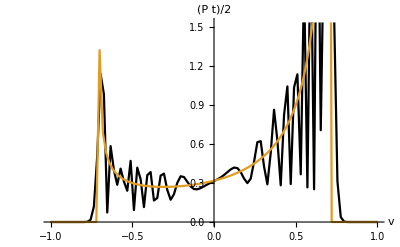

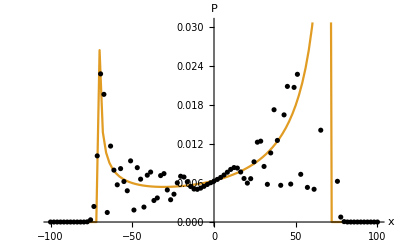

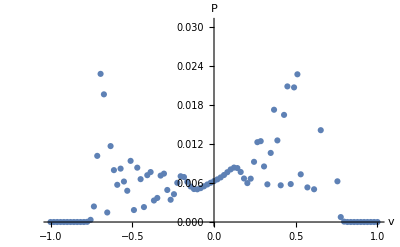

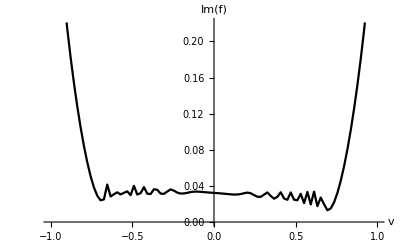

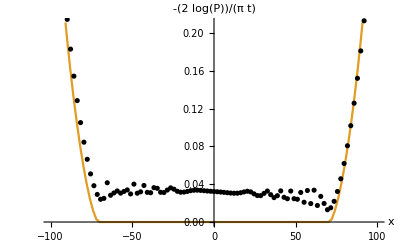

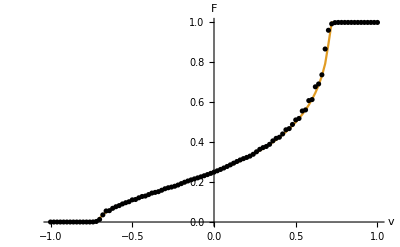

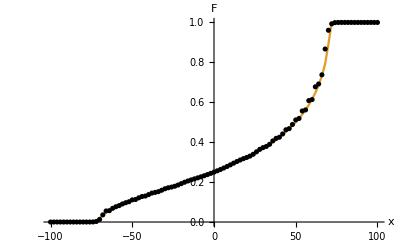

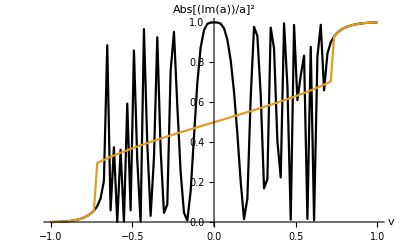

```mathematica
(* In arXiv:2007.12879v1 this were Figures 5, 8, 10 *)
(* The graph of a conjectural weak limit of Im^a(vt,t)/|a(vt,t)|^2.
For |v|>1/Sqrt[2] we approximate the limit of the sequence just by the t=1000-th element.
    For |v|<1/Sqrt[2] we plot the main term given in Problem 2. *)
m=1;
e=1; 
xmax=100; (* Rebooting of Mathematica is required to change xmax *)
(* In the following formula, (y-x)/e must be even *)
a1[x_,y_]:=(1/(1+m^2e^2)^((y/e-1)/2))If[Abs[x]>=y,0,Sum[Binomial[(x+y-2e)/(2e),r]Binomial[(y-x-2e)/(2e),r](m e)^(2r+1)(-1)^r,{r,0,y/(2e)}]];
a2[x_,y_]:=(1/(1+m^2e^2)^((y/e-1)/2)) If[x==y>0,1,
Sum[Binomial[(x+y-2e)/(2e),r]Binomial[(y-x-2e)/(2e),r-1](m e)^(2r)(-1)^r,{r,1,y/(2e)}]];
theta[x_,y_]:=y/e ArcSin[(m e)/(√((1+m^2 e^2)(1-(x/y)^2)))]-x/e ArcSin[(m e x/y)/(√(1-(x/y)^2))]+π/4;
p[x_,t_]:=(a1[x,t]^2+a2[x,t]^2);
limitp[v_]:=1/(Pi(1-v)√(1-(1+1)(v)^2));
corr[x_,t_]:=a2[x,t]^2/(a1[x,t]^2+a2[x,t]^2);
limitcorr[v_]:=If[v==0,1/2,1-(Sqrt[1-v^2]-(1-v))/(2v)];
f[0]=0.0;
f[x_]:=f[x-2]+a1[x-xmax,xmax]^2+a2[x-xmax,xmax]^2;
limitf[v_]:=ArcCos[(1-2 v)/(Sqrt[2](1-v))]/Pi;
(* To compare the main term with the true weak limit, we integrate both corr[vt,t] and the main term over v. *)
g[-xmax]=0.0;
g[x_]:=g[x-2]+corr[x,xmax];
limitg[v_]:=1/2 (v-√(1-v^2)+Log[1+√(1-v^2)]);
limitfree[v_]:=2/Pi (2v Log[v/(√2)+√(v^2-1/2)]-2 Log[1/(√2)+√(v^2-1/2)]+(1-v)Log[1-v^2]-2v Log[1/(√2)]);
normalization=N[2g[0]/(xmax)];
step1height=N[2g[-2Floor[xmax/(2Sqrt[2])]]/(xmax)];
step2height=N[2g[2Floor[xmax/(2Sqrt[2])]]/(xmax)];
tablep=Table[(xmax/2) N[p[x,xmax]],{x,-xmax+2,xmax-2,2}];
tablefree=Table[-2/(Pi xmax) N[Log[p[x,xmax]]],{x,-xmax+2,xmax-2,2}];

tablelimitp=Table[If [Abs[x]<xmax/Sqrt[2],N[limitp[x/xmax]],If[Abs[x]==Ceiling[xmax/Sqrt[2]],2xmax,0]],{x,-xmax,xmax,2}];
tablelimitf=Table[If [Abs[x]<xmax/Sqrt[2],N[limitf[x/xmax]],HeavisideTheta[x]],{x,-xmax,xmax,2}];
tablelimitfree=Table[If [Abs[x]>xmax/Sqrt[2],N[limitfree[Abs[x/xmax]]],0],{x,-xmax,xmax,2}];
tablecorr=Table[N[corr[x,xmax]],{x,-xmax+2,xmax-2,2}];
tablef=Table[N[f[x]],{x,0,2xmax,2}];
tablecombined=Table[If [Abs[x]<xmax/Sqrt[2],N[limitcorr[x/xmax]],N[corr[x,xmax]]],{x,-xmax+2,xmax-2,2}];
tableg=Table[N[2g[x]/xmax],{x,-xmax,xmax,2}]; tablelimitg=Table[If [Abs[x]<xmax/Sqrt[2],N[limitg[x/xmax]-limitg[-1/Sqrt[2]]+step1height],N[2g[x]/xmax]+HeavisideTheta[x](limitg[1/Sqrt[2]]-limitg[-1/Sqrt[2]]+step1height-step2height)],{x,-xmax,xmax,2}];
ListPlot[{tablep,tablelimitp},Joined->{True,True},PlotStyle->{Black,Default},DataRange->{-1,1},AxesLabel->{v,1/2t P}]
ListPlot[{(2/xmax)tablep,(2/xmax)tablelimitp},Joined->{False,True},PlotStyle->{Black,Default},DataRange->{-xmax,xmax},AxesLabel->{x,P}]
ListPlot[{(2/xmax)tablep},Joined->False,PlotStyle->Default,DataRange->{-1,1},AxesLabel->{v,P}]
ListPlot[{tablefree},Joined->{True},DataRange->{-1,1},PlotStyle->Black,AxesLabel->{v,Im[f]}]
ListPlot[{tablefree,tablelimitfree},Joined->{False,True},PlotStyle->{Black,Default},DataRange->{-xmax,xmax},AxesLabel->{x,-(2Log[P])/(Pi t)}]
ListPlot[{tablef,tablelimitf},Joined->{False,True},PlotStyle->{Black,Default},DataRange->{-1,1},AxesLabel->{v,F}]
ListPlot[{tablef,tablelimitf},Joined->{False,True},PlotStyle->{Black,Default},DataRange->{-xmax,xmax},AxesLabel->{x,F}]
ListPlot[{tablecorr,tablecombined},Joined->{True,True},PlotStyle->{Black,Default},DataRange->{-1,1},AxesLabel->{v,Abs[Im[a]/a]^2}]
ListPlot[{tableg,tablelimitg},Joined->{False,True},PlotStyle->{Black,Default},DataRange->{-1,1},AxesLabel->{v,G}]
```

```mathematica
16.Plots in Figure  12
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

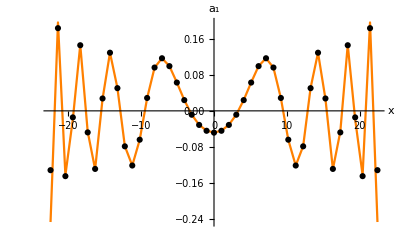

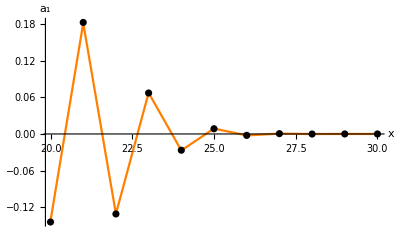

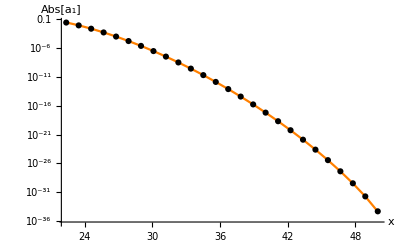

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

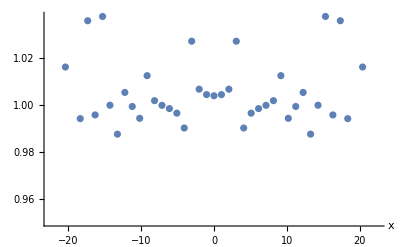

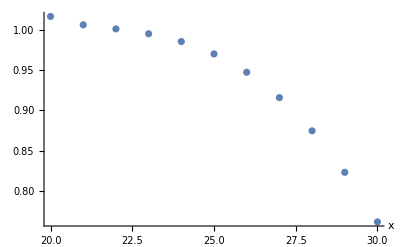

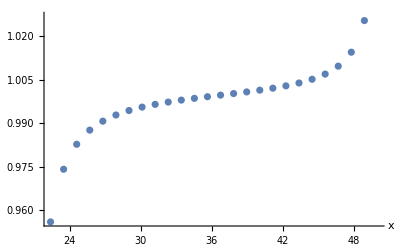

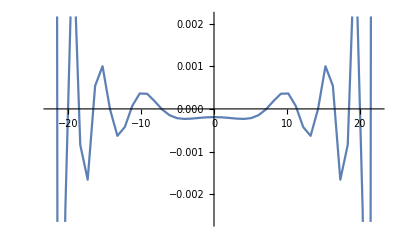

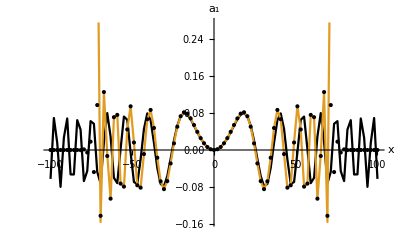

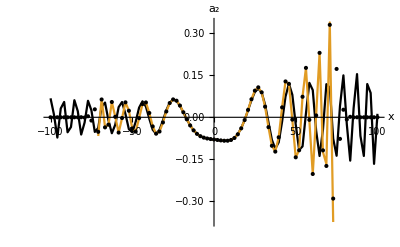

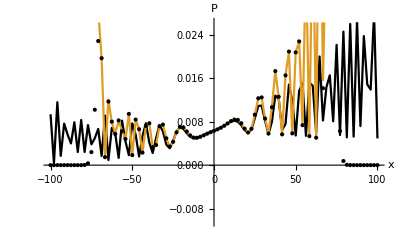

```mathematica
(* In arXiv:2007.12879v1 this were Figures 11-12 *)
(* Never use float numbers here *)
m=4;ε=1/2;y=100ε; left=40y/100;right=60y/100;
(* In the following formula, (t-x)/e must be even *)
a1[x_,y_,m_,e_]:=(1/(1+m^2e^2)^((y/e-1)/2))If[x==y,0,Sum[Binomial[(x+y-2e)/(2e),r]Binomial[(y-x-2e)/(2e),r](m e)^(2r+1)(-1)^r,{r,0,y/(2e)}]];
a2[x_,y_,m_,e_]:=(1/(1+m^2e^2)^((y/e-1)/2)) If[x==y>0,1,
Sum[Binomial[(x+y-2e)/(2e),r]Binomial[(y-x-2e)/(2e),r-1](m e)^(2r)(-1)^r,{r,1,y/(2e)}]];

largea1[x_,y_,m_,ε_]:=ε √((2m)/(π y))(1-(1+m^2 ε^2)(x/y)^2)^(-1/4)Sin[y/ε ArcSin[(m ε)/(√((1+m^2 ε^2)(1-(x/y)^2)))]-x/ε ArcSin[(m ε x/y)/(√(1-(x/y)^2))]+π/4];
largea2[x_,y_,m_,ε_]:=ε √((2m)/(π y))(1-(1+m^2 ε^2)(x/y)^2)^(-1/4)√((y+x)/(y-x))Cos[y/ε ArcSin[(m ε)/(√((1+m^2 ε^2)(1-(x/y)^2)))]-x/ε ArcSin[(m ε x/y)/(√(1-(x/y)^2))]+π/4];
smalla1[x_,t_]:=Sqrt[2/(Pi t)]Sin[Pi t/4-x^2/(2 t)];
smalla2[x_,t_]:=Sqrt[2/(Pi t)] Cos[Pi t/4-x^2/(2 t)]+2Sqrt[1/(Pi t)]x/t Cos[Pi (t+1)/4-x^2/(2 t)];
approxa1[x_,y_,m_,ε_]:=(-1)^((y-ε-x-ε)/(2ε))ε √(m/(2π (y-ε)))((1+m^2 ε^2)(x/(y-ε))^2-1)^(-1/4)Exp[-(y-ε) (-2 ArcCosh[(m ε)/(√((1+m^2 ε^2)(1-(x/(y-ε))^2)))]+2Abs[x/(y-ε)]ArcCosh[(m ε Abs[x/(y-ε)])/(√(1-(x/(y-ε))^2))])/(2ε)];
airya1[x_,t_,m_,ε_]:=m ε(-1)^((t-ε-x-ε)/(2ε))( 2/(m ^2ε(t-ε)))^(1/3)AiryAi[ ( 2/(m ^2ε(t-ε)))^(1/3)(Sqrt[1+m^2ε^2]x-t+ε)/ε];
airya2[x_,t_,m_,ε_]:=(Sqrt[1+m^2ε^2]+1)(-1)^((t-x)/(2ε))( 2/(m ^2ε(t-ε)))^(1/3)AiryAi[ ( 2/(m ^2ε(t-ε)))^(1/3)(Sqrt[1+m^2ε^2](x-ε)-t+ε)/ε];
ListPlot[{Table[If [Abs[x]<y/√(1+m^2 ε^2),a1[x,y,m,ε],1/0],{x,-y+2ε,y-2ε,2ε}],Table[If [Abs[x]<y/√(1+m^2 ε^2),largea1[x,y-ε,m,ε],1/0],{x,-y+2ε,y-2ε,2ε}]}, Joined->{False,True},PlotStyle->{Black,Orange},DataRange->{-y,y},AxesLabel->{x,Subscript[a, 1]},LabelStyle->Directive[FontSize->Tiny]]
ListPlot[{Table[a1[x,y,m,ε],{x,left,right,2ε}],Table[airya1[x,y,m,ε],{x,left,right,2ε}]},Joined->{False,True},PlotStyle->{Black,Orange},DataRange->{left,right},AxesLabel->{x,Subscript[a, 1]},LabelStyle->Directive[FontSize->Tiny]]
ListPlot[{Table[Abs[a1[x,y,m,ε]],{x,2Floor[y/(2ε Sqrt[1+m^2ε^2])]ε+4ε,y-2ε,2ε}]
,Table[Abs[approxa1[x,y,m,ε]],{x,2Floor[y/(2ε Sqrt[1+m^2ε^2])]ε+4ε,y-2ε,2ε}]},Joined->{False,True},PlotStyle->{Black,Orange},DataRange->{y/√(1+m^2 ε^2),y},AxesLabel->{x,Abs[Subscript[a, 1]]},ScalingFunctions->"Log",LabelStyle->Directive[FontSize->Tiny]]
ListPlot[{Table[If [Abs[x]<y/√(1+m^2 ε^2),a1[x,y,m,ε]/largea1[x,y-ε,m,ε],1/0],{x,-y+2ε,y-2ε,2ε}]}, Joined->False,DataRange->{-y,y},AxesLabel->{x},LabelStyle->Directive[FontSize->Tiny]]
ListPlot[Table[a1[x,y,m,ε]/airya1[x,y,m,ε],{x,left,right,2ε}],Joined->False,DataRange->{left,right},AxesLabel->{x},LabelStyle->Directive[FontSize->Tiny]]
ListPlot[{Table[a1[x,y,m,ε]/approxa1[x,y,m,ε],{x,2Floor[y/(2ε Sqrt[1+m^2ε^2])]ε+4ε,y-2ε,2ε}]}, Joined->False,DataRange->{y/( Sqrt[1+m^2ε^2]),y},AxesLabel->{x},LabelStyle->Directive[FontSize->Tiny]]

ListPlot[{Table[a1[x,y,m,ε]-largea1[x,y-ε,m,ε],{x,-y+2ε,y-2ε,2ε}]}, Joined->True,DataRange->{-y,y},AxesLabel->Automatic,LabelStyle->Directive[FontSize->Tiny]]
ListPlot[{Table[smalla1[x,100],{x,-100+2,100-2,2}],Table[largea1[x,100-1,1,1],{x,-100+2,100-2,2}], Table[a1[x,100,1,1],{x,-100+2,100-2,2}]},Joined->{True,True,False},PlotStyle->{Black,Default,Black},DataRange->{-100,100},AxesLabel->{x,Subscript[a, 1]}](*LabelStyle->Directive[FontSize->Tiny]]*)
ListPlot[{Table[smalla2[x,100],{x,-100+4,100-4,2}],Table[largea2[x-1,100-1,1,1],{x,-100+4,100-4,2}],Table[a2[x,100,1,1],{x,-100+4,100-4,2}]},Joined->{True,True,False},PlotStyle->{Black,Default,Black},DataRange->{-100,100},AxesLabel->{x,Subscript[a, 2]}]
ListPlot[{Table[smalla1[x,100]^2+smalla2[x,100]^2,{x,-100+4,100-4,2}],Table[largea1[x,100-1,1,1]^2+largea2[x-1,100-1,1,1]^2,{x,-100+4,100-4,2}],Table[a1[x,100,1,1]^2+a2[x,100,1,1]^2,{x,-100+4,100-4,2}]}, Joined->{True,True,False},PlotStyle->{Black,Default,Black},DataRange->{-100,100},AxesLabel->{x,P}]
```

```mathematica
17.Plots in Figure  15
```

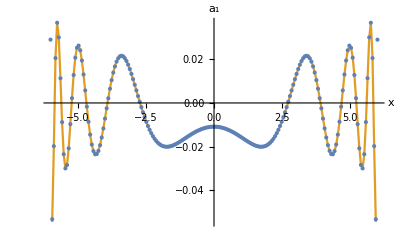

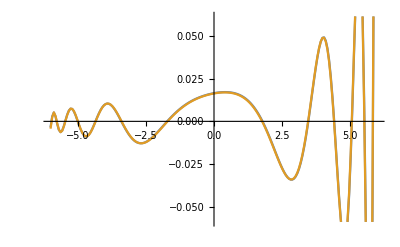

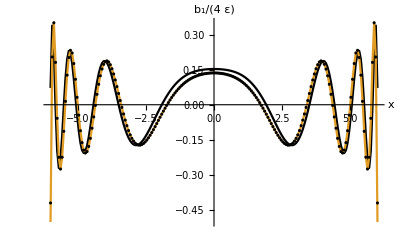

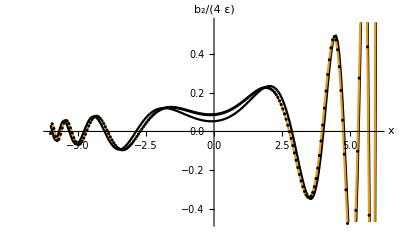

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.489293}. NIntegrate obtained 1.35385×10^-8+1.14353×10^-13 ⅈ and 9.87737×10^-14 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.489293}. NIntegrate obtained 9.36982×10^-9-5.19584×10^-14 ⅈ and 9.59704×10^-14 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.489293}. NIntegrate obtained 6.5075×10^-9+6.30607×10^-14 ⅈ and 9.81233×10^-14 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

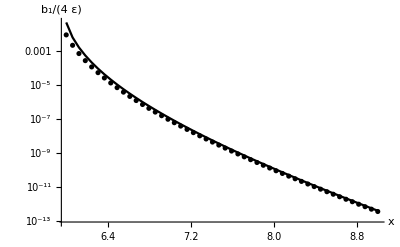

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {102.468}. NIntegrate obtained 7.81983×10^-9+9.01917×10^-14 ⅈ and 3.10707×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {102.468}. NIntegrate obtained 5.30734×10^-9-6.68701×10^-14 ⅈ and 3.23501×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {4.40245×10^-7}. NIntegrate obtained 3.61795×10^-9-3.80217×10^-14 ⅈ and 3.18702×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

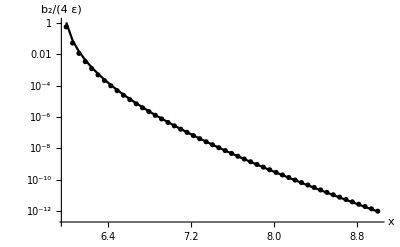

```mathematica
(* In arXiv:2007.12879v1 this was Figure 15 *)
m=4;ε=3/100;y=200ε;
w[p_,m_,e_]:=(1/e)ArcCos[Cos[p e]/Sqrt[1+m^2e^2]];
(* In the following formula, (t-x)/e must be odd *)
b1[x_,t_,m_,e_]:=Re[m e^2/(Pi Sqrt[1+m^2e^2]) NIntegrate[Cos[w[p,m,e](t-e)]Exp[-I p x]/Sin[w[p,m,e]e],{p,0,Pi/e}]];

b2[x_,t_,m_,e_]:= Re[e/Pi NIntegrate[(-Sin[w[p,m,e](t-e)]+I Cos[w[p,m,e](t-e)]Sin[p e]/( Sqrt[1+m^2e^2]Sin[w[p,m,e]e]))Exp[-I p (x-e)],{p,0,Pi/e}]];
largeb1[x_,y_,m_,ε_]:=ε √((2m)/(π y))(1-(1+m^2 ε^2)(x/y)^2)^(-1/4)Cos[y/ε ArcSin[(m ε)/(√((1+m^2 ε^2)(1-(x/y)^2)))]-x/ε ArcSin[(m ε x/y)/(√(1-(x/y)^2))]+π/4];
largeb2[x_,y_,m_,ε_]:=-ε √((2m)/(π y))(1-(1+m^2 ε^2)(x/y)^2)^(-1/4)√((y+x)/(y-x))Sin[y/ε ArcSin[(m ε)/(√((1+m^2 ε^2)(1-(x/y)^2)))]-x/ε ArcSin[(m ε x/y)/(√(1-(x/y)^2))]+π/4];
feynman1[x_,t_,m_]:= -(m /4) BesselY[0,m Sqrt[t^2-x^2]];
feynman2[x_,t_,m_]:= (m /4) (x+t)/Sqrt[t^2-x^2]BesselY[1,m Sqrt[t^2-x^2]];
feynman3[x_,t_,m_]:= m /(2Pi) BesselK[0,m Sqrt[x^2-t^2]];
feynman4[x_,t_,m_]:= m /(2Pi) (x+t)/Sqrt[x^2-t^2]BesselK[1,m Sqrt[x^2-t^2]];ListPlot[{Table[a1[x,y,m,ε],{x,-y+2ε,y-2ε,2ε}],Table[largea1[x,y-ε,m,ε],{x,-y+2ε,y-2ε,2ε}]}, Joined->{False,True},DataRange->{-y,y},AxesLabel->{x,Subscript[a, 1]},LabelStyle->Directive[FontSize->Tiny]]
ListPlot[{Table[a2[x,y,m,ε],{x,-y+4ε,y-4ε,2ε}],Table[largea2[x-ε,y-ε,m,ε],{x,-y+4ε,y-4ε,2ε}]}, Joined->True,DataRange->{-y,y}]
ListPlot[{Table[feynman1[x,y,m],{x,-y+3ε,y-3ε,2ε}],Table[largeb1[x,y-ε,m,ε]/(4ε),{x,-y+3ε,y-3ε,2ε}],Table[b1[x,y,m,ε]/(4ε),{x,-y+3ε,y-3ε,2ε}]}, Joined->{True,True,False},PlotStyle->{Black,Default,Black},DataRange->{-y,y},AxesLabel->{x,Subscript[b, 1]/(4"ε")}]
ListPlot[{Table[feynman2[x,y,m],{x,-y+3ε,y-3ε,2ε}],Table[largeb2[x-ε,y-ε,m,ε]/(4ε),{x,-y+3ε,y-3ε,2ε}],Table[b2[x,y,m,ε]/(4ε),{x,-y+3ε,y-3ε,2ε}]}, Joined->{True,True,False},PlotStyle->{Black,Default,Black},DataRange->{-y,y},AxesLabel->{x,Subscript[b, 2]/(4"ε")}]
ListPlot[{Table[feynman3[x,y,m],{x,y+ε,1.5y,2ε}],Table[b1[x,y,m,ε]/(4ε),{x,y+ε,1.5y,2ε}]}, Joined->{True,False},PlotStyle->{Black,Black},DataRange->{y,1.5y},AxesLabel->{x,Subscript[b, 1]/(4"ε")},ScalingFunctions->"Log"]
ListPlot[{Table[feynman4[x,y,m],{x,y+ε,1.5y,2ε}],Table[b2[x,y,m,ε]/(4ε),{x,y+ε,1.5y,2ε}]}, Joined->{True,False},PlotStyle->{Black,Black},DataRange->{y,1.5y},AxesLabel->{x,Subscript[b, 2]/(4"ε")},ScalingFunctions->"Log"]
```

## 18. Checking of Corollary 3

```mathematica
(* Here we check the last equality from the proof of Corollary 3*)
(* We use notation from the paper by Sunada-Tate, 2012 *)
phi1=0;
phi2=1;
lambda=Abs[phi2]^2-Abs[phi1]^2+2Re[a b Conjugate[phi1]phi2]/Abs[a]^2;
a=1/Sqrt[1+m^2e^2];
b=m e/Sqrt[1+m^2e^2];
A[xi_]:=(Abs[phi2]^2-Abs[phi1]^2-Abs[a]^2lambda)xi Sqrt[Abs[a]^2-xi^2]/(Abs[a]^2Abs[b]);
B[xi_]:=-(xi^2+Abs[a]^2lambda xi )/(Abs[a]^2);
FullSimplify[Sqrt[A[xi]^2+B[xi]^2]-(1+xi)Abs[xi]/Abs[a],-1<xi<1&&0<m&&0<e]
```

0

## 19. Plots in Figure 6

The plots in Figure 6 are computed on IBM quantum-computing website.

Circuit link: 
https://quantum-computing.ibm.com/composer/files/new?initial=N4IgdghgtgpiBcIBiMCeYoTAAgMYAsZcBrGAJwGdsKBLALxmwGZqAXGABypdggoFcyMWGFZUATCAA0IAI58oCEAHkACgFEAcgEUAggGUAstnEA6AAwBuADpgaYXABt%2BAE0bW5MRzQBGARlN7XA8bMFtZIQBzbFkAbSYAXVDcKLx4pNtbfBjY8wyHXAAPHLypOL8EstjxfKKSyvL87Li85LqWhtiKqprk4o6qitDm3Nr20cHO3ttx0sbQ3gEhHIrsAFoAPjSh20XBRjia9a3caqTpEDcKFJoOVhoAezAlEABfIA

Output link:
https://quantum-computing.ibm.com/jobs/61b72085de9f247b22713acc

Computation of theoretical distribution link: 
https://quantum-computing.ibm.com/jobs/61b4bf5978707cd185f62e6b

QASM code:

OPENQASM 2.0;
include “qelib1.inc”;

qreg q[3];
creg c[3];

h q[0];
ccx q[0],q[1],q[2];
cx q[0],q[1];
h q[0];
ccx q[0],q[1],q[2];
cx q[0],q[1];
h q[0];
ccx q[0],q[1],q[2];
cx q[0],q[1];
measure q[1] -> c[1];
measure q[2] -> c[2];

## 20. Plots in Figure 1

```mathematica
(*FIGURE 1 middle and right*)
nmax=400;(*even number*)nmaxtoshow=200;
m=200;(*mass*)SubPlus[kernel][n_,k_]:=((nmax/2)/(1+m^2/nmax^2)^((n-1)/2)) If[k==n,1,Sum[Binomial[(n+k)/2-1,r] Binomial[(n-k)/2-1,r-1] (m/nmax)^(2 r) (-1)^r,{r,1,n/2}]];
SubMinus[kernel][n_,k_]:=((nmax/2)/(1+m^2/nmax^2)^((n-1)/2)) If[k==n,0,Sum[Binomial[(n+k)/2-1,r] Binomial[(n-k)/2-1,r] (m/nmax)^(2 r+1) (-1)^r,{r,0,n/2}]];
(*Table[(2/nmax)Subscript[kernel,+][2,k],{k,0,2,2}] Table[(2/nmax)Subscript[kernel,-][2,k],{k,0,2,2}]*)
SubPlus[TableK]=Table[SubPlus[kernel][nmax,k],{k,2-nmax,nmax-2,2}];
SubMinus[TableK]=Table[SubMinus[kernel][nmax,k],{k,2-nmax,nmax-2,2}];
tablep=Table[If[Abs[k]≥n,0,N[4 (SubMinus[kernel][n,k]^2+SubPlus[kernel][n,k]^2)/nmax^2]],{n,0,nmax,2},{k,2-nmax,nmax-2,2}];
delta=0.2;
ListContourPlot[tablep,DataRange->{{-nmaxtoshow,nmaxtoshow},{0,nmaxtoshow}},AxesLabel->Automatic,AspectRatio->1/2,ContourStyle->None,PlotLegends->Automatic,LabelStyle->Directive[FontSize->Tiny]]
ContourPlot[If[Abs[x]>y-0.01 nmaxtoshow,0,(m/2)^2 (BesselJ[0,m Sqrt[y^2-x^2]/nmaxtoshow]^2+((y+x)^2/(y^2-x^2)) BesselJ[1,m Sqrt[y^2-x^2]/nmaxtoshow]^2)],{x,-nmaxtoshow,nmaxtoshow},{y,0,nmaxtoshow},AspectRatio->1/2,ContourStyle->None,PlotLegends->Automatic,LabelStyle->Directive[FontSize->Tiny]]
```